```mathematica
latoQuadrato=10
```

10

```mathematica
Polinomio1=x^2+y^2-10^2
```

-100+x^2+y^2

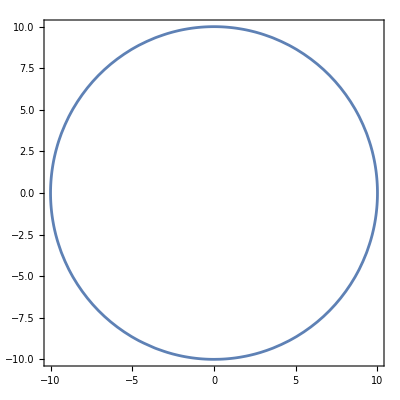

```mathematica
plot1=ContourPlot[Polinomio1==0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

```mathematica
Polinomio2=(x-3)^4+(y+5)^2-2^2
```

-4+(-3+x)^4+(5+y)^2

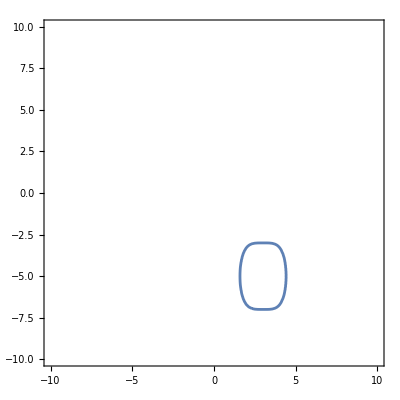

```mathematica
plot2=ContourPlot[Polinomio2==0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

```mathematica
Polinomio3=(x^2+y^2)^2-50*(x^2-y^2)
```

-50 (x^2-y^2)+(x^2+y^2)^2

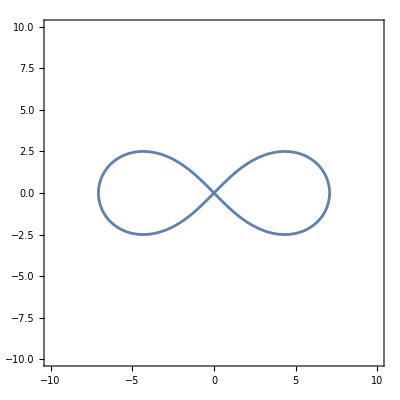

```mathematica
plot3=ContourPlot[Polinomio3==0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

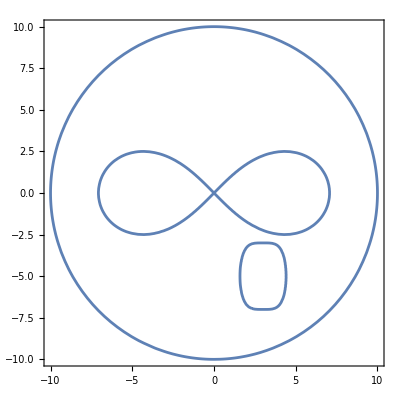

```mathematica
Show[plot1,plot2,plot3]
```

```mathematica
Polinomio=Polinomio1*Polinomio2*Polinomio3
```

(-100+x^2+y^2) (-4+(-3+x)^4+(5+y)^2) (-50 (x^2-y^2)+(x^2+y^2)^2)

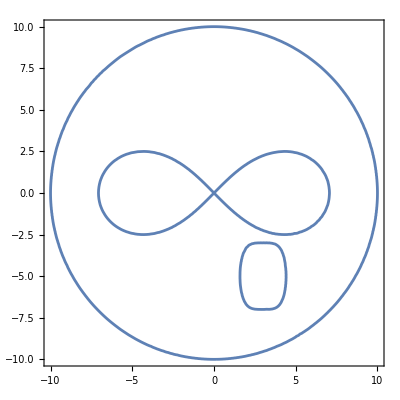

```mathematica
plot4=ContourPlot[Polinomio==0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

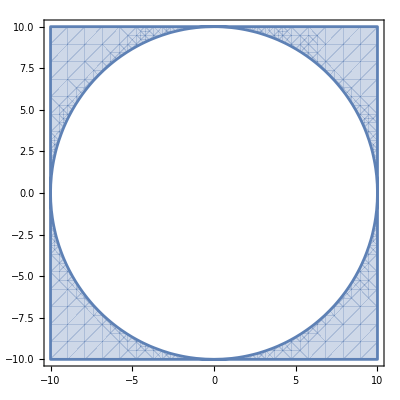

```mathematica
RegionPlot[Polinomio1≥0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

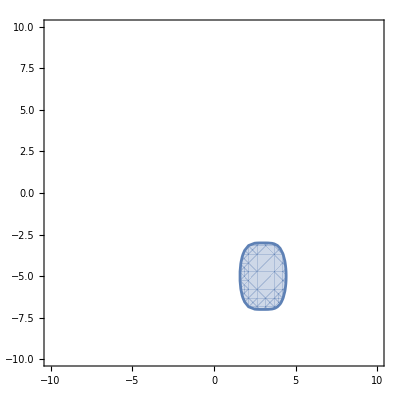

```mathematica
RegionPlot[Polinomio2<=0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

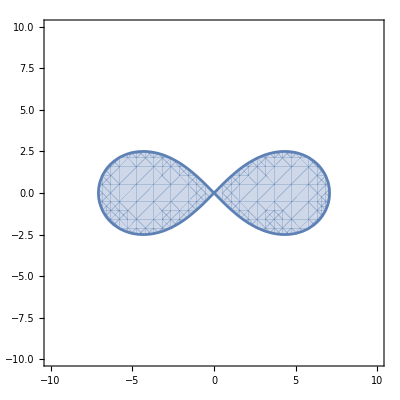

```mathematica
RegionPlot[Polinomio3<=0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

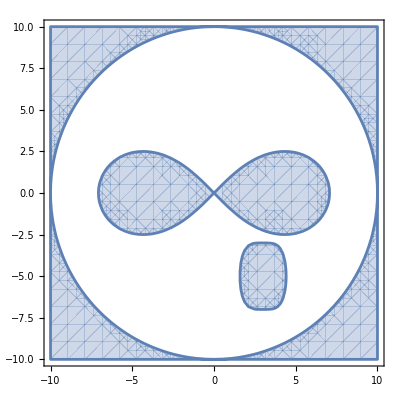

```mathematica
R1=RegionPlot[Polinomio1>=0||Polinomio2<=0||Polinomio3<=0,{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato}]
```

```mathematica
px=D[Polinomio,x]
py=D[Polinomio,y]
```

(-100+x^2+y^2) (-4+(-3+x)^4+(5+y)^2) (-100 x+4 x (x^2+y^2))+4 (-3+x)^3 (-100+x^2+y^2) (-50 (x^2-y^2)+(x^2+y^2)^2)+2 x (-4+(-3+x)^4+(5+y)^2) (-50 (x^2-y^2)+(x^2+y^2)^2)

(-100+x^2+y^2) (-4+(-3+x)^4+(5+y)^2) (100 y+4 y (x^2+y^2))+2 (5+y) (-100+x^2+y^2) (-50 (x^2-y^2)+(x^2+y^2)^2)+2 y (-4+(-3+x)^4+(5+y)^2) (-50 (x^2-y^2)+(x^2+y^2)^2)

```mathematica
tangentiVerticali=NSolve[{Polinomio==0,py==0},{x,y},Reals]
```

{{x→-10.,y→0.},{x→10.,y→0.},{x→7.07107,y→0.},{x→-7.07107,y→0.},{x→1.58579,y→-5.},{x→4.41421,y→-5.},{x→0.,y→0.},{x→0.,y→0.}}

```mathematica
tangentiVerticali1={x,y}/.tangentiVerticali
```

{{-10.,0.},{10.,0.},{7.07107,0.},{-7.07107,0.},{1.58579,-5.},{4.41421,-5.},{0.,0.},{0.,0.}}

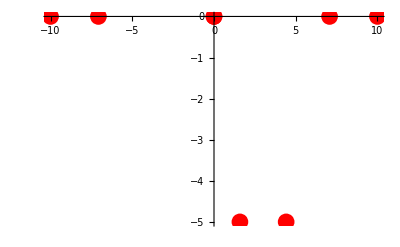

```mathematica
plot5=ListPlot[tangentiVerticali1,PlotStyle->Directive[Red,PointSize[0.03]]]
```

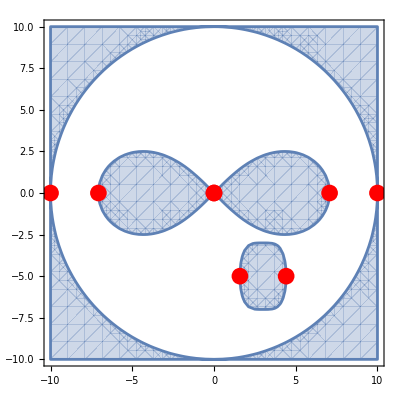

```mathematica
R2=Show[R1,plot5]
```

```mathematica
R3=R2;
Do[
punto=tangentiVerticali1[[i]];
puntoBasso={punto[[1]],-latoQuadrato};
puntoAlto={punto[[1]],latoQuadrato};
L1=ListLinePlot[{puntoBasso,puntoAlto},PlotStyle->Directive[Red,Dashed]];
R3=Show[R3,L1];
,{i,1,Length[tangentiVerticali1]}]
```

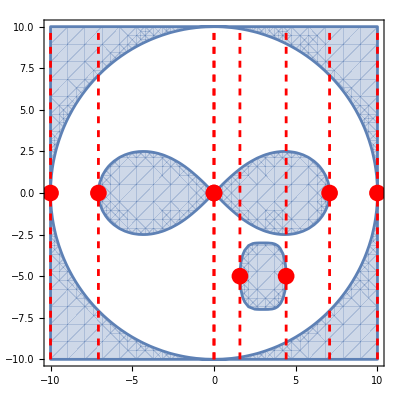

```mathematica
R3
```

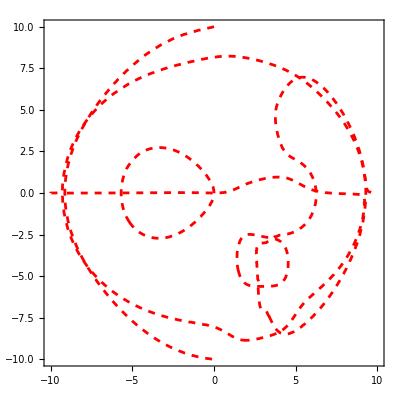

```mathematica
plot6=ContourPlot[{px==0,py==0},{x,-latoQuadrato,latoQuadrato},{y,-latoQuadrato,latoQuadrato},ContourStyle->Directive[Red,Dashed]]
```

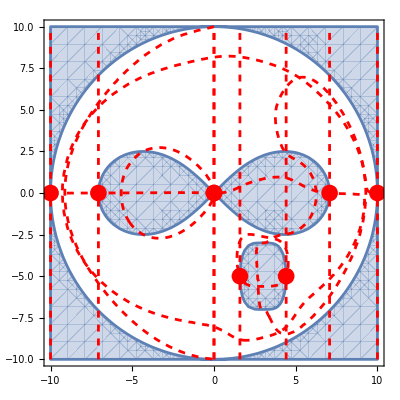

```mathematica
R4=Show[R3,plot6]
```

```mathematica
puntiN1=NSolve[{px==0,py==0},{x,y},Reals];
```

```mathematica
puntiN2=NSolve[{px==0,Polinomio==0},{x,y},Reals];
```

```mathematica
puntiN=Join[puntiN1,puntiN2];
```

```mathematica
punti={x,y}/.puntiN;
```

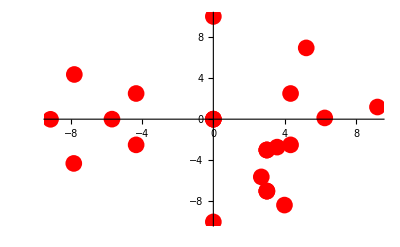

```mathematica
plot7=ListPlot[punti,PlotStyle->Directive[Red,PointSize[0.03]]]
```

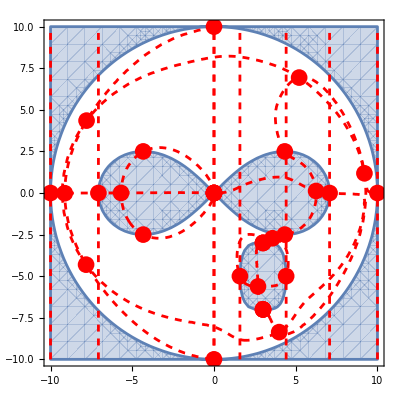

```mathematica
R5=Show[R4,plot7]
```

```mathematica
puntiNN={};
Do[
puntiN3=NSolve[{px==0,x==Rationalize[tangentiVerticali1[[i]][[1]],0.00001]},{x,y},Reals];
puntiN4=NSolve[{py==0,x==Rationalize[tangentiVerticali1[[i]][[1]],0.00001]},{x,y},Reals];
puntiN5=NSolve[{Polinomio==0,x==Rationalize[tangentiVerticali1[[i]][[1]],0.00001]},{x,y},Reals];

puntiNN=Join[puntiNN,puntiN3,puntiN4,puntiN5];
,{i,1,Length[tangentiVerticali1]}]
punti={x,y}/.puntiNN;
```

{{-10.,0},{-10.,0},{-10.,0},{10.,0},{10.,0},{10.,0},{7.07107,-6.21164},{7.07107,5.92979},{7.07107,-5.17664},{7.07107,1.45241×10^-7},{7.07107,5.31989},{7.07107,-7.07107},{7.07107,-0.00293071},{7.07107,0.00293071},{7.07107,7.07107},{-7.07107,-5.42809},{-7.07107,5.41843},{-7.07107,-5.17303},{-7.07107,4.16609×10^-9},{-7.07107,5.1785},{-7.07107,-7.07107},{-7.07107,-0.00293071},{-7.07107,0.00293071},{-7.07107,7.07107},{1.58578,-10.296},{1.58578,53.3471},{1.58578,-8.81209},{1.58578,-4.99999},{1.58578,-2.88865},{1.58578,0.369167},{1.58578,8.1823},{1.58578,-9.87346},{1.58578,-1.44587},{1.58578,1.44587},{1.58578,9.87346},{4.41422,-8.48578},{4.41422,-2.4851},{4.41422,2.4},{4.41422,6.36248},{4.41422,-8.0546},{4.41422,-4.99999},{4.41422,-3.39729},{4.41422,0.907268},{4.41422,7.37927},{4.41422,-8.973},{4.41422,-2.49893},{4.41422,2.49893},{4.41422,8.973},{0,-10.},{0,0},{0,0},{0,10.},{0,-8.05692},{0,0},{0,8.16559},{0,-10.},{0,0},{0,0},{0,10.},{0,-10.},{0,0},{0,0},{0,10.},{0,-8.05692},{0,0},{0,8.16559},{0,-10.},{0,0},{0,0},{0,10.}}

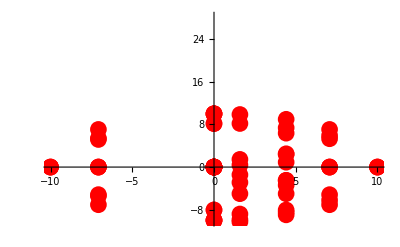

```mathematica
plot8=ListPlot[punti,PlotStyle->Directive[Red,PointSize[0.03]]]
```

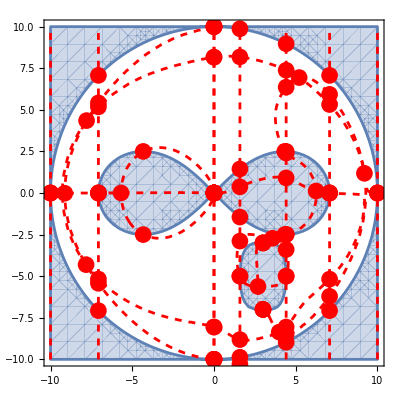

```mathematica
R6=Show[R5,plot8]
```